```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_copper_312run8.txt","Table"];
```

```mathematica
num=Dimensions[rawdata][[1]];
```

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
timevolt=Table[0,{i,num}];
Do[timevolt[[i]]=Flatten[{time[[i]],voltage[[i]]},2],{i,1,num}]
```

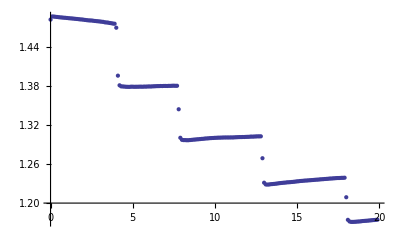

```mathematica
ListPlot[Take[timevolt,{1,200}]]
```

```mathematica
threshold=.005;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+3,i+7}]][[1]]}}]}],{i,num-7}]
```

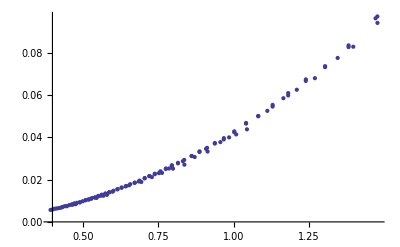

```mathematica
ListPlot[dT]
```

```mathematica
threshold=.005;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{Print[timevolt[[i]]],Print[Mean[Take[voltage,{i-5,i}]]-Mean[Take[voltage,{i+2,i+7}]]],dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+2,i+7}]][[1]]}}]}],{i,num-7}]
```